## SimShow-example.nb SimShow, SimShowAt, SimShowFinal

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (10-Nov-2012)) loaded Sun 11 Nov 2012 10:20:38
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.90 (2-Nov-2012) loaded Sun 11 Nov 2012 10:20:41
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

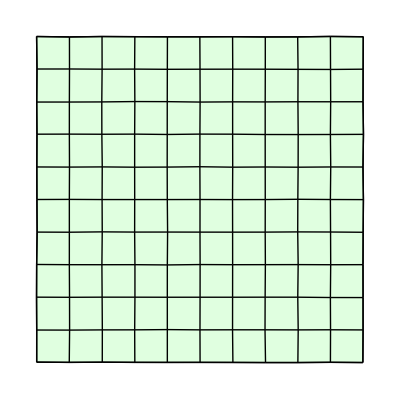

```mathematica
w=TemplateRectangular[10,10];
w=RandomizeTemplate[w, 0.01];
ShowTissue[w]
```

The following network is a mass-action implementation of the simple harmonic oscillator.

```mathematica
net = {{X+Y-> X, k1/Y[t]}, {Y-> Y+X, k2}};
parameters = {k1-> 1, k2-> 1}; 
interpret[net]/.parameters
```

{{X'[t]==Y[t],Y'[t]==-X[t]},{X,Y}}

```mathematica
s=run[net/.parameters, initialConditions-> {X-> 1, Y-> 1}, timeSpan-> 10]
```

{{X→InterpolatingFunction[{{0.,10.}},<>],Y→InterpolatingFunction[{{0.,10.}},<>]}}

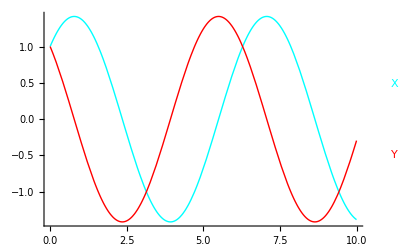

```mathematica
runPlot[s]
```

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net, "Diffusion"-> {{X, DX}}];
```

100 Cells.

2 internal reactions in each cell.

200 intracellular reactions.

360 diffusion reactions.

560 total reactions.

```mathematica
myic=Table[{X[i]-> RandomReal[{-1,1}], Y[i]-> RandomReal[{-1,1}]}, {i, 1, 100}]//Flatten;
```

```mathematica
sim=RunSim[bignet/.{DX-> .5}, parameters, myic, {0,2}];
```

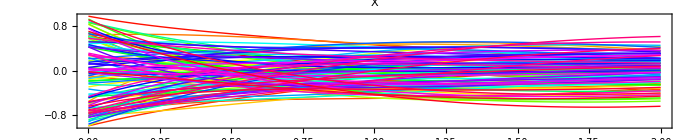

```mathematica
SimPlot[sim,X, AspectRatio-> .2, ImageSize-> 700]
```

Use SimShowFinal to show the concentrations at the end of the simulation with automatic scaling.

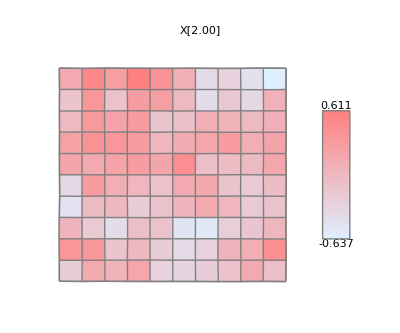

```mathematica
SimShowFinal[sim,X, w, {LightBlue, Pink}, "EdgeStyles"-> Gray]
```

Use SimShow to show a snapshot of the solution at a given time

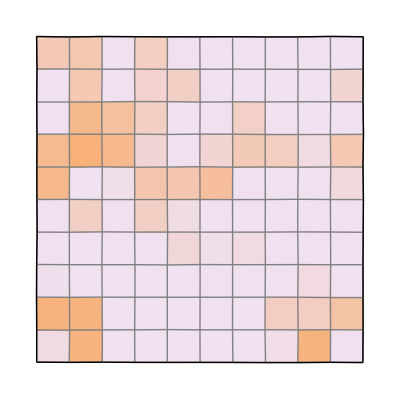

```mathematica
SimShow[sim, X, 1, w, {LightPurple, Orange}, {0, 1}, "EdgeStyles"-> Gray]
```

Use SimShowAt to show a legend

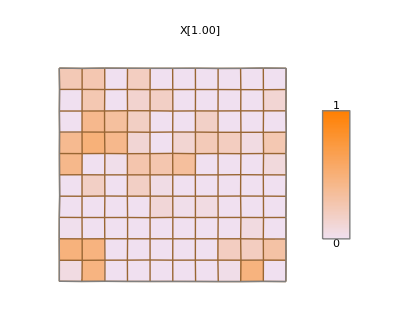

```mathematica
SimShowAt[sim, X, 1, w, {LightPurple, Orange}, {0, 1}, "EdgeStyles"-> Brown]
```

Use SimeShowAt to Show a legend and Autoscale the Range

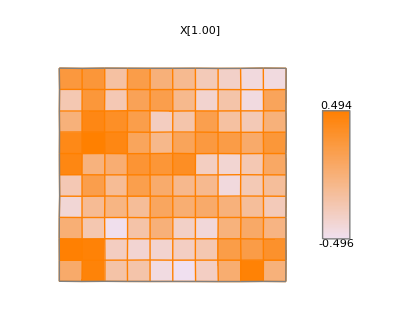

```mathematica
SimShowAt[sim, X, 1, w, {LightPurple, Orange}, "EdgeStyles"-> Orange]
```